```mathematica
dir="D:\\betterEnergy"
```

D:\betterEnergy

```mathematica
GetDetritusEnergies[frameNo_]:=Module[{path,file,headings,items,applyHeading,ptE},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
ptE={"pt","e"}/.items;
Cases[ptE,{2,x_}->x]
]
```

48400

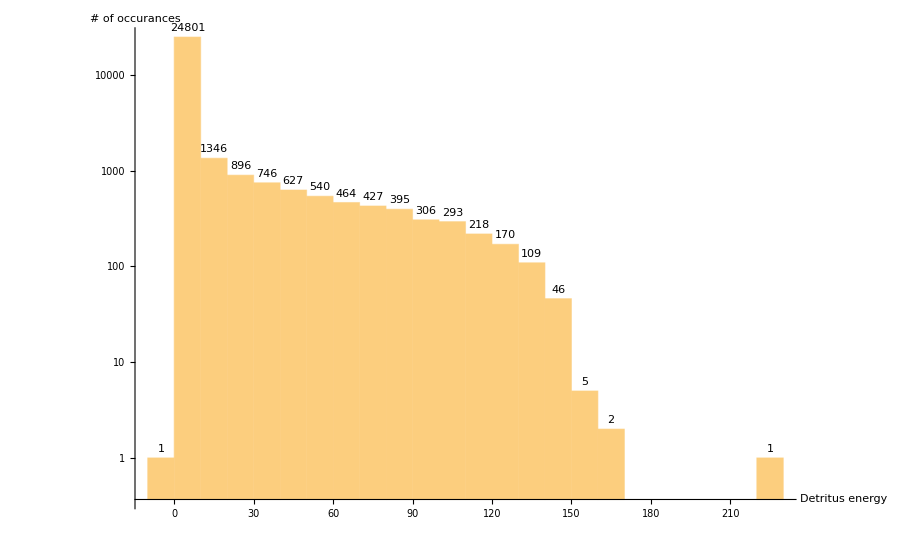

Mean: | 13.8233
Median: | 2.90149
Max: | 220.755

```mathematica
frame=48400
es =GetDetritusEnergies[frame];
Histogram[es,30,
PlotRange->All,
ScalingFunctions->"Log",
AxesLabel->{"Detritus energy","# of occurances"},
LabelingFunction->Above,
ImageSize->900]
({{"Mean:", es//Mean}, {"Median:", es//Median}, {"Max:", es//Max}})//TableForm
```

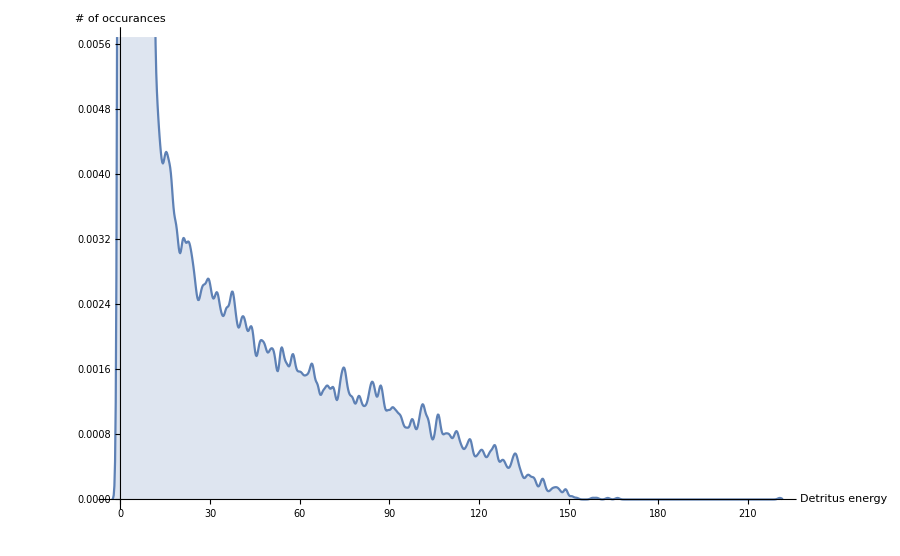

```mathematica
SmoothHistogram[es,
AxesLabel->{"Detritus energy","# of occurances"},
Filling->Bottom,
ImageSize->900]
```

```mathematica
RandomSample[es,10]
```

{1.06337,2.73598,0.959989,0.521968,1.43112,1.25078,1.3868,0.260168,1.39124,0.334962}

```mathematica
(CountsBy[es,#<1&][True])/(es//Length)//N
```

0.125482

```mathematica
<|False->37775,True->6030|>[True]
```

6030